NDSolve::nderr: Error test failure at t == 3.75615; unable to continue.

{{d→InterpolatingFunction[{{0.,3.75615}},<>],x→InterpolatingFunction[{{0.,3.75615}},<>],m→InterpolatingFunction[{{0.,3.75615}},<>],c→InterpolatingFunction[{{0.,3.75615}},<>],a→InterpolatingFunction[{{0.,3.75615}},<>]}}

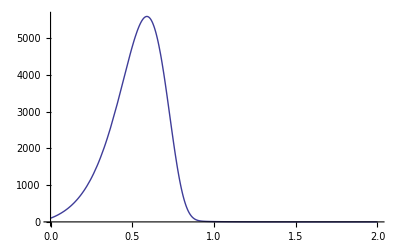

```mathematica
sol1=NDSolve[{d'[t]==0.0000926*d[t]*c[t]*a[t]-.000075*x[t]*d[t],x'[t]==1000+ 0.0000926*x[t]*c[t]*a[t]-.0009*x[t]*d[t]-.005*x[t]*m[t],m'[t]==0.0000339*m[t]*c[t]*a[t]-.00005*x[t]*m[t], c'[t]== 0.000227*c[t](1-(c[t]/1000)),a'[t]== 0.0001135*a[t]*(1-(a[t]/1000)), d[0]==100,x[0]==100,m[0]==50,c[0]==200,a[0]==400},{d,x,m,c,a},{t,0,24}]

Plot[Evaluate[{x[t]}/.sol1],{t,0,2}]
```

{{d→InterpolatingFunction[{{0.,24.}},<>],m→InterpolatingFunction[{{0.,24.}},<>],c→InterpolatingFunction[{{0.,24.}},<>],a→InterpolatingFunction[{{0.,24.}},<>]}}

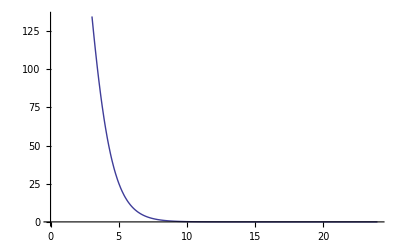

```mathematica
sol1=NDSolve[{d'[t]==0.0000926*d[t]*c[t]*a[t],m'[t]==0.0000339*m[t]*c[t]*a[t], c'[t]== c[t](1-(c[t]/1000)),a'[t]==0.0001135*a[t]*(1-(a[t]/1000)), d[0]==100,m[0]==50,c[0]==200,a[0]==400},{d,m,c,a},{t,0,24}]

Plot[Evaluate[{c'[t]}/.sol1],{t,0,24}]
```

{{d→InterpolatingFunction[{{0.,24.}},<>],x→InterpolatingFunction[{{0.,24.}},<>],m→InterpolatingFunction[{{0.,24.}},<>],a→InterpolatingFunction[{{0.,24.}},<>]}}

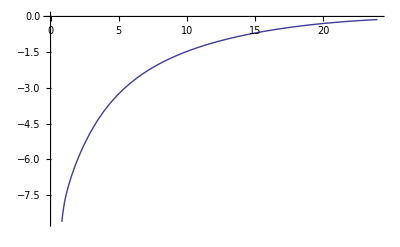

```mathematica
sol1=NDSolve[{d'[t]==0.0000926*d[t]*a[t]-.0025*x[t]*d[t],x'[t]== 0.0000926*x[t]*a[t]-.0025*x[t]*d[t]-.15*x[t]*m[t],m'[t]==0.0000339*m[t]*a[t]-.15*x[t]*m[t],a'[t]== 0.0001135*a[t]*(1-(a[t]/1000)), d[0]==100,x[0]==100,m[0]==50,a[0]==400},{d,x,m,a},{t,0,24}]

Plot[Evaluate[{x'[t]}/.sol1],{t,0,24}]
```

{{d→InterpolatingFunction[{{0.,24.}},<>],x→InterpolatingFunction[{{0.,24.}},<>],m→InterpolatingFunction[{{0.,24.}},<>],c→InterpolatingFunction[{{0.,24.}},<>]}}

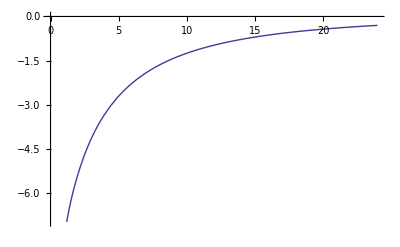

```mathematica
sol1=NDSolve[{d'[t]==0.0000926*d[t]*c[t]*-.0025*x[t]*d[t],x'[t]== 0.0000926*x[t]*c[t]-.0025*x[t]*d[t]-.15*x[t]*m[t],m'[t]==0.0000339*m[t]*c[t]-.15*x[t]*m[t], c'[t]== 0.000227*c[t](1-(c[t]/1000)), d[0]==100,x[0]==100,m[0]==50,c[0]==200},{d,x,m,c},{t,0,24}]

Plot[Evaluate[{x'[t]}/.sol1],{t,0,24}]
```

```mathematica
sol1=NDSolve[{x'[t]== 0.0000926*x[t]*c[t]*a[t]-.15*x[t]*m[t],m'[t]==0.0000339*m[t]*c[t]*a[t]-.15*x[t]*m[t], c'[t]== 0.000227*c[t](1-(c[t]/1000)),a'[t]== 0.0001135*a[t]*(1-(a[t]/1000)), x[0]==100,m[0]==50,c[0]==200,a[0]==400},{x,m,c,a},{t,0,24}]

Plot[Evaluate[{x'[t]}/.sol1],{t,0,24}]
```

NDSolve::nderr: Error test failure at t == 6.84024; unable to continue.

{{x→InterpolatingFunction[{{0.,6.84024}},<>],m→InterpolatingFunction[{{0.,6.84024}},<>],c→InterpolatingFunction[{{0.,6.84024}},<>],a→InterpolatingFunction[{{0.,6.84024}},<>]}}

-Graphics-

NDSolve::nderr: Error test failure at t == 4.93206; unable to continue.

{{d→InterpolatingFunction[{{0.,4.93206}},<>],x→InterpolatingFunction[{{0.,4.93206}},<>],c→InterpolatingFunction[{{0.,4.93206}},<>],a→InterpolatingFunction[{{0.,4.93206}},<>]}}

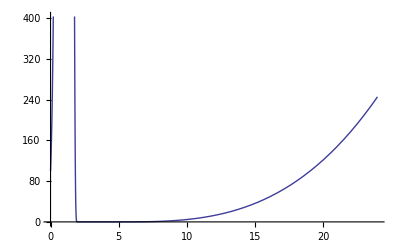

```mathematica
sol1=NDSolve[{d'[t]==0.0000926*d[t]*c[t]*a[t]-.0025*x[t]*d[t],x'[t]== 0.0000926*x[t]*c[t]*a[t]-.0025*x[t]*d[t]-.15, c'[t]== 0.000227*c[t](1-(c[t]/1000)),a'[t]==0.0001135*a[t]*(1-(a[t]/1000)), d[0]==100,x[0]==100,c[0]==200,a[0]==400},{d,x,c,a},{t,0,24}]

Plot[Evaluate[{x[t]}/.sol1],{t,0,24}]
```

```mathematica
sol1=NDSolve[{d'[t]==0.0000926*d[t]*c[t]*a[t],m'[t]==0.0000339*m[t]*c[t]*a[t], c'[t]== 0.000227*c[t](1-(c[t]/1000)),a'[t]==0.0001135*a[t]*(1-(a[t]/1000)), d[0]==100,m[0]==50,c[0]==200,a[0]==200},{d,m,c,a},{t,0,24}]

Plot[Evaluate[{d[t]}/.sol1],{t,0,24}]
```

{{d→InterpolatingFunction[{{0.,24.}},<>],m→InterpolatingFunction[{{0.,24.}},<>],c→InterpolatingFunction[{{0.,24.}},<>],a→InterpolatingFunction[{{0.,24.}},<>]}}

-Graphics-